# Supplementary tensors

## ITensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.048622,Null}

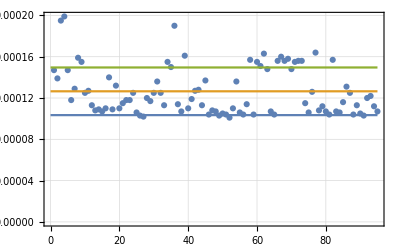

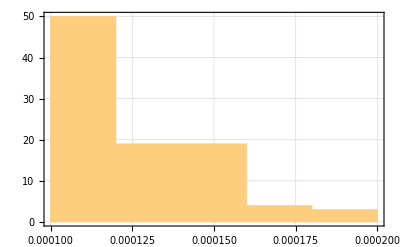

{0.000103433,0.000126505,0.000149578}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[2]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.0692,Null}

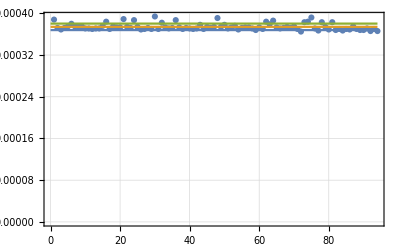

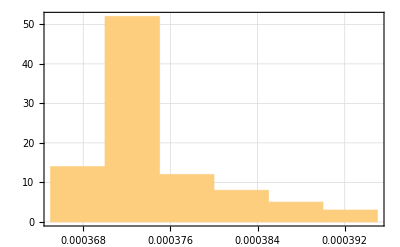

{0.000367874,0.000374085,0.000380296}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[3]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.606302,Null}

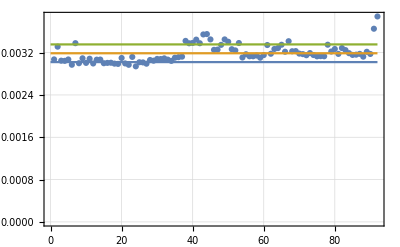

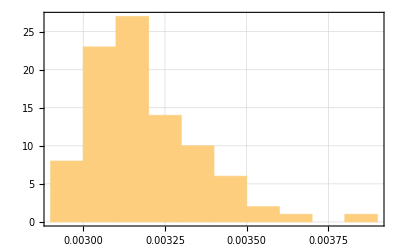

{0.00302107,0.00318825,0.00335543}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[4]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{4.56907,Null}

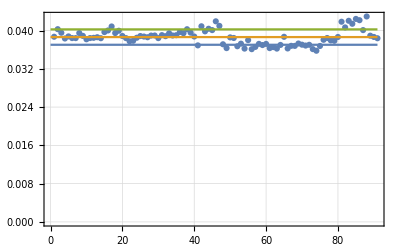

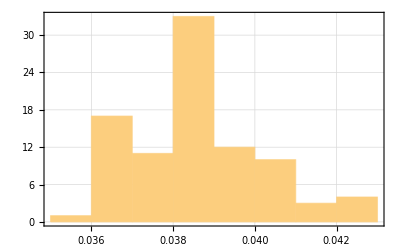

{0.0370236,0.0386322,0.0402407}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[5]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.084624,Null}

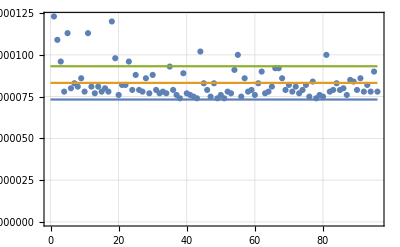

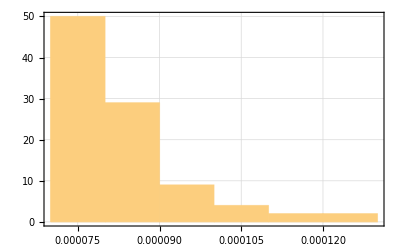

{0.0000732624,0.0000832292,0.0000931959}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.110088,Null}

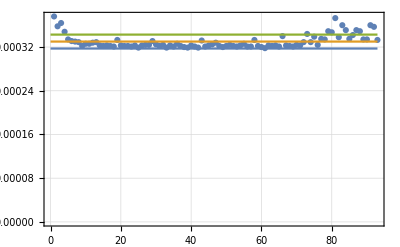

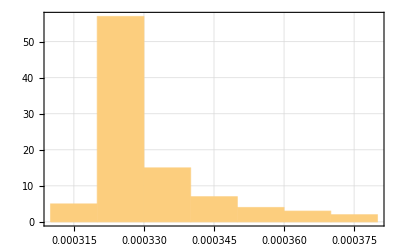

{0.000317303,0.000330043,0.000342783}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.41195,Null}

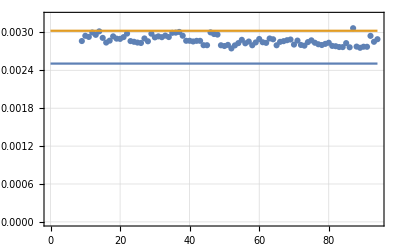

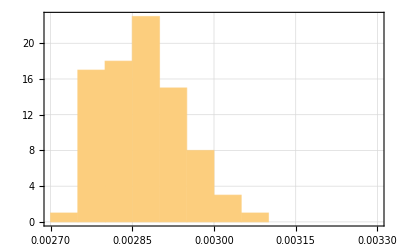

{0.00250597,0.00302551,0.00354505}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{4.36968,Null}

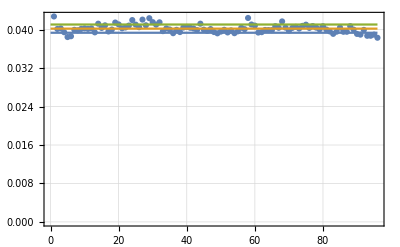

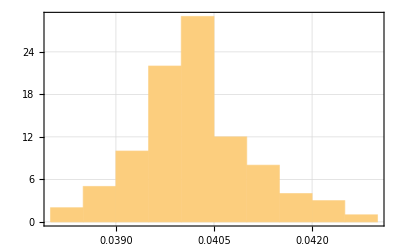

{0.0393566,0.0402146,0.0410727}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{79.4024,Null}

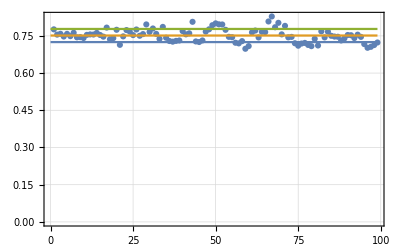

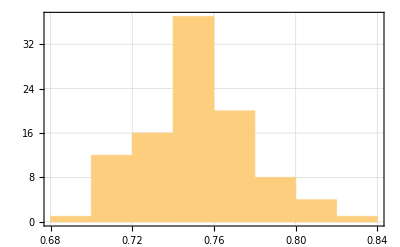

{0.724956,0.751425,0.777893}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C1Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.104706,Null}

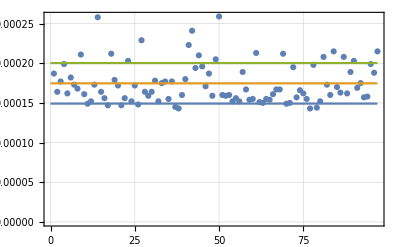

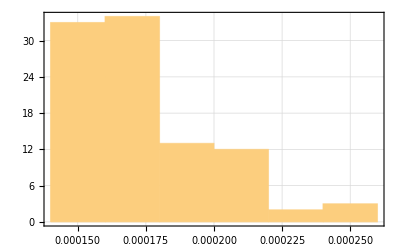

{0.000149147,0.00017468,0.000200214}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.150713,Null}

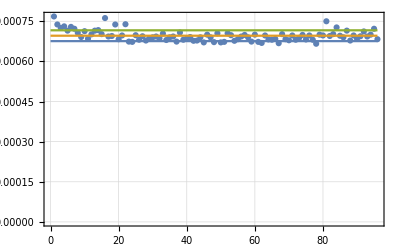

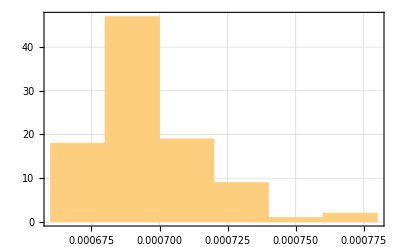

{0.000675767,0.000696,0.000716233}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.928289,Null}

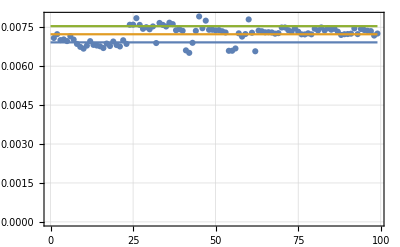

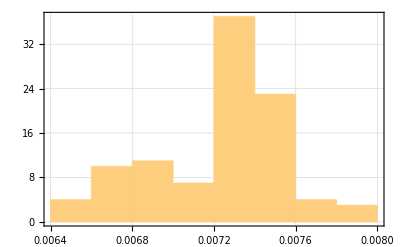

{0.00691574,0.00722825,0.00754076}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{10.3792,Null}

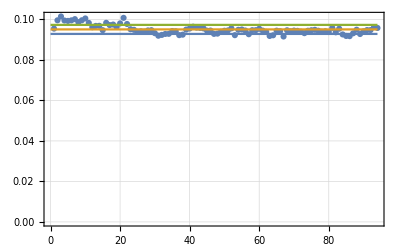

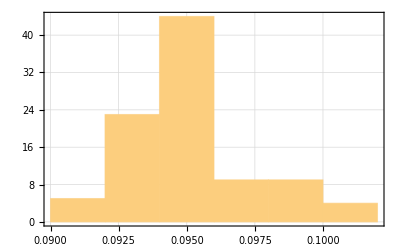

{0.0928524,0.0950857,0.097319}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{293.6,Null}

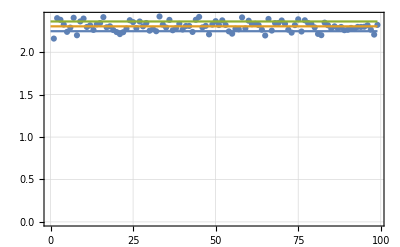

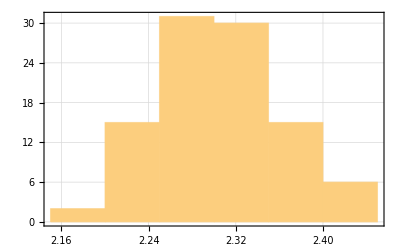

{2.24794,2.30537,2.3628}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C2Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{1.06755,Null}

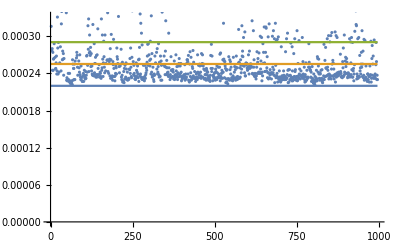

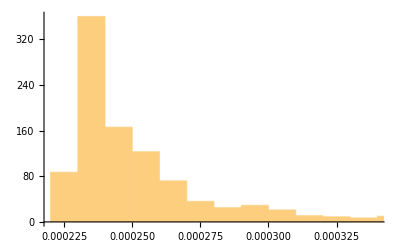

{0.0002199,0.000255194,0.000290488}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.54918,Null}

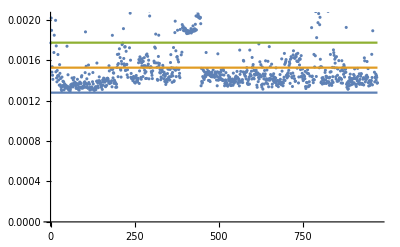

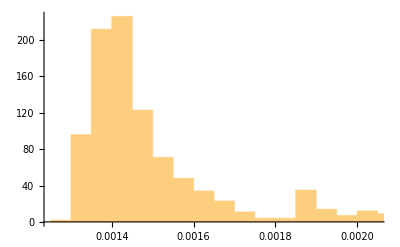

{0.00127807,0.00152521,0.00177234}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{19.316,Null}

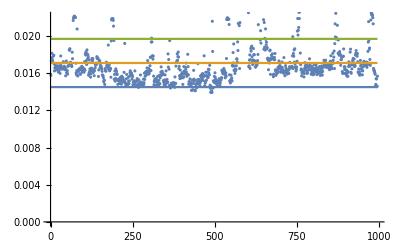

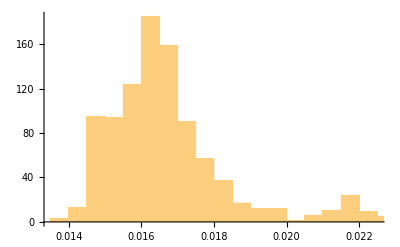

{0.0145118,0.0171051,0.0196984}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1180.35,Null}

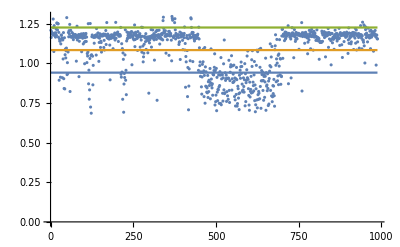

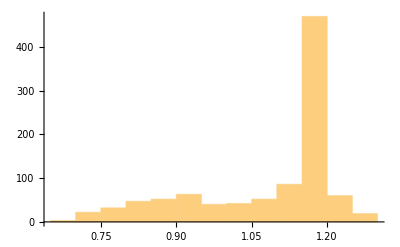

{0.941158,1.08346,1.22575}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{61.4356,Null}

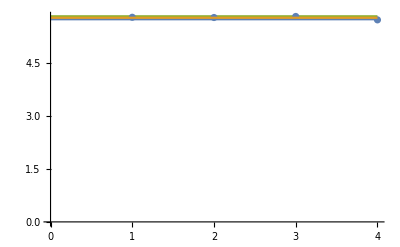

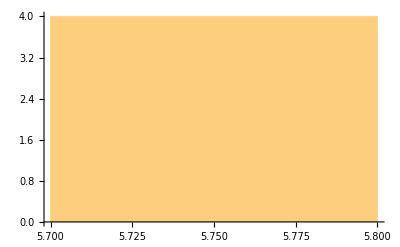

{5.72136,5.76274,5.80412}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{5.10487,Null}

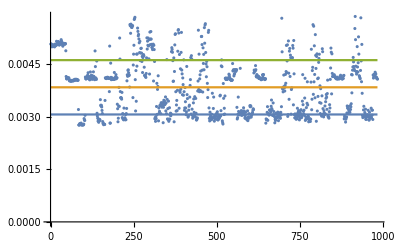

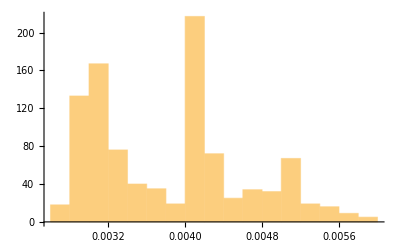

{0.00307052,0.00384711,0.0046237}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{11.1889,Null}

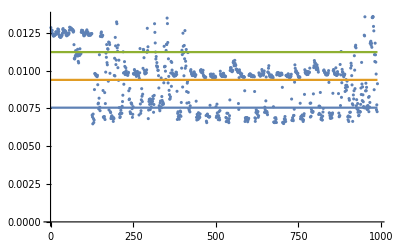

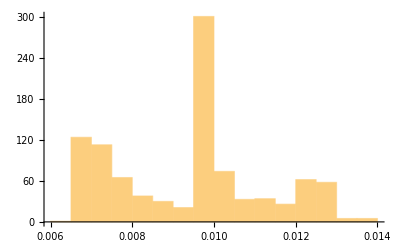

{0.00755279,0.00939085,0.0112289}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{25.4708,Null}

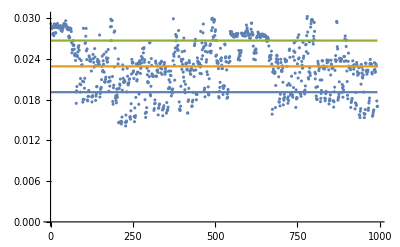

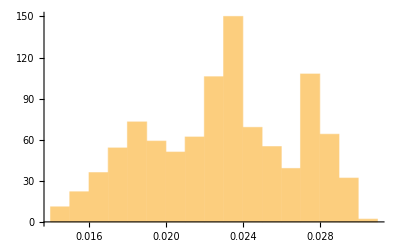

{0.0191183,0.0229208,0.0267233}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{45.0122,Null}

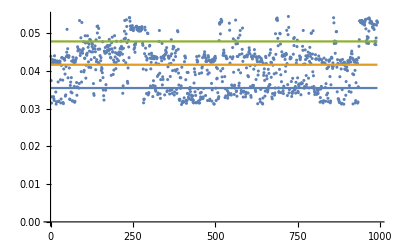

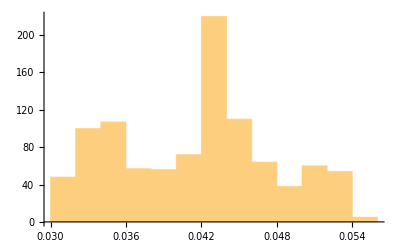

{0.0354542,0.041623,0.0477919}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{510.463,Null}

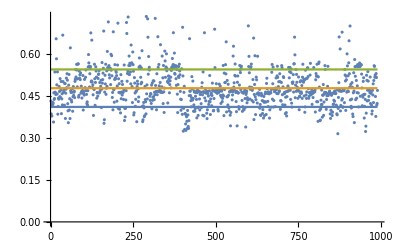

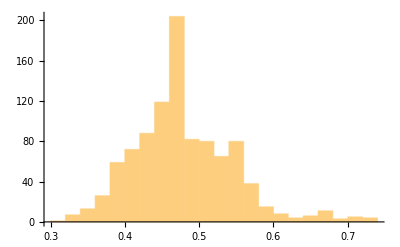

{0.41111,0.478122,0.545135}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## Kinetic term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{6.45373,Null}

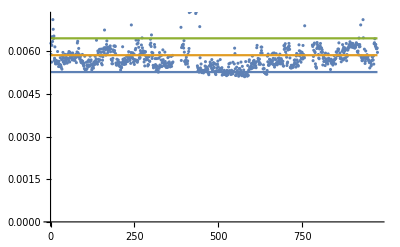

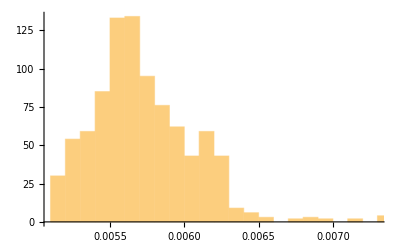

{0.00526386,0.00585657,0.00644929}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{24.3775,Null}

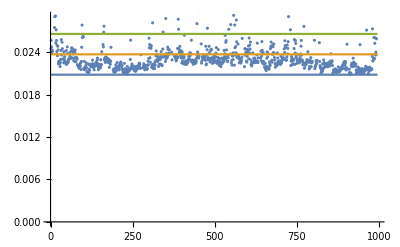

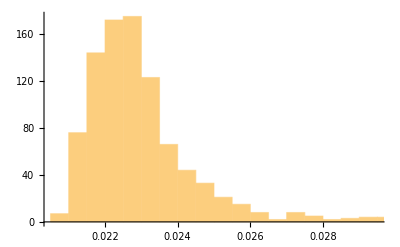

{0.0208288,0.0237105,0.0265921}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{218.296,Null}

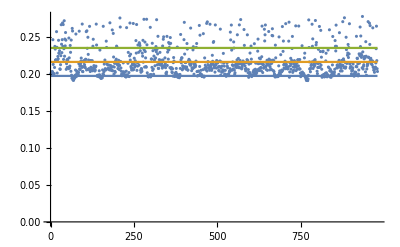

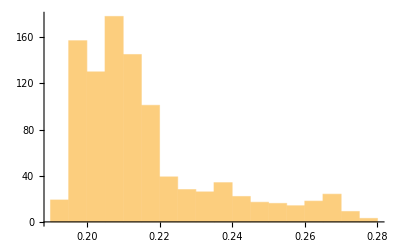

{0.19693,0.215799,0.234667}

```mathematica
theData = {};
For[i=1,i<=1000,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

## Potential term

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.000471,0.000626,0.003192,0.038478,0.714088}

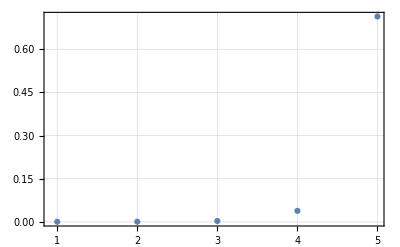

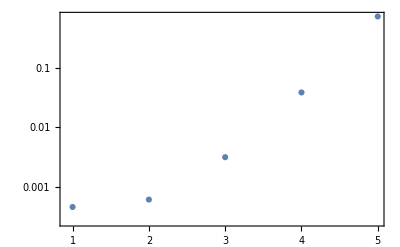

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
Table[Timing[GravitonScalarPotentialVertex[DummyArray[n],λ]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

# Graviton-fermion vertex

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.005099,0.021947,0.364244,3.58896,150.084}

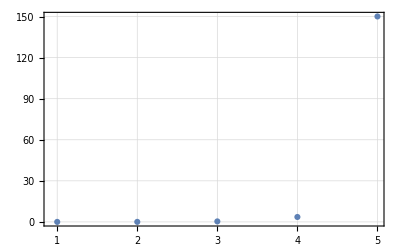

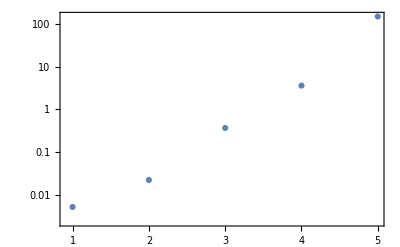

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
<<DummyArray`
Table[Timing[GravitonFermionVertex[DummyArray[n],p1,p2,m]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

# Graviton-vector vertices

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## Massive vectors

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.035743,0.232109,3.09437,54.7461,893.594}

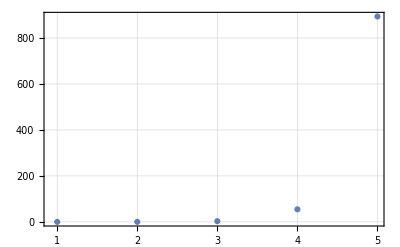

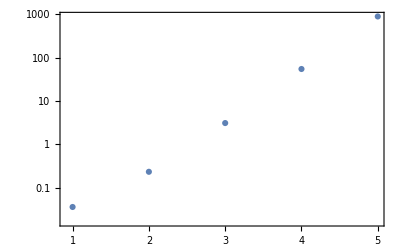

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
Table[Timing[GravitonMassiveVectorVertex[DummyArray[n],λ1,p1,λ2,p2,m]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Massless vectors

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.058493,0.674379,12.5426,372.343}

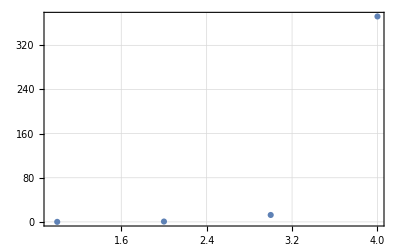

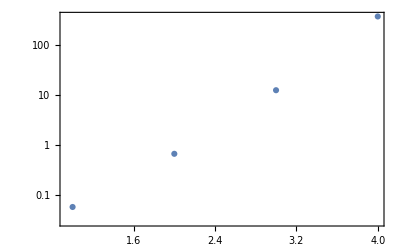

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
Table[Timing[GravitonVectorVertex[DummyArrayK[n],λ1,p1,λ2,p2,ε]][[1]],{n,4}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Ghosts

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.004132,0.017367,0.18074,2.4578,43.0992}

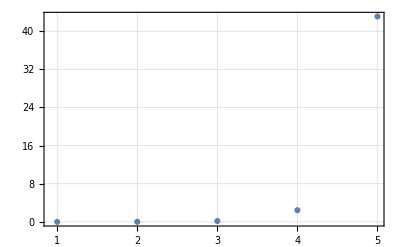

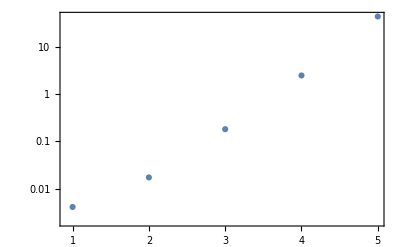

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
Table[Timing[GravitonVectorGhostVertex[DummyArray[n],p1,p2]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

# Graviton vertices

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## Pure graviton vertices

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{6.58279,297.311}

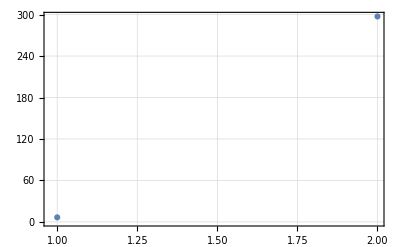

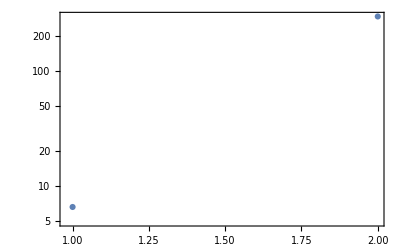

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
Table[Timing[GravitonVertex[DummyArrayK[n],ε]][[1]],{n,3,4}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Graviton-ghost vertex

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.050258,0.958687,18.7448,505.261}

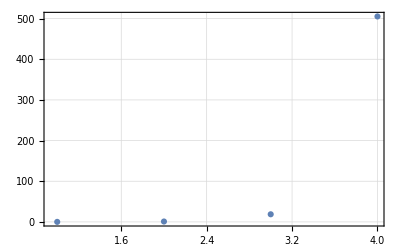

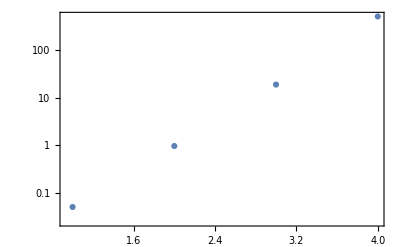

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
Table[Timing[GravitonGhostVertex[DummyArrayK[n],λ1,p1,λ2,p2]][[1]],{n,1,4}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```